```mathematica
Orange
orange=Blend[{Orange,Red},0.2]
Blue
blue=Blend[{Blue,Black},0.2]
```

RGBColor[1, 0.5, 0]

RGBColor[1., 0.4, 0.]

RGBColor[0, 0, 1]

RGBColor[0., 0., 0.8]

```mathematica
(*---------------Funtions for normal---------------*)
δn[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])*Exp[-(p-q)^2/(2*Subscript[k, 1]^2)];
ρn[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])*Exp[-p^2/(2*Subscript[k, 2]^2)];
μn[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])*Exp[-q^2/(2*Subscript[k, 3]^2)];
G1n[ϕ1_,p_,q_,u_,v_]:=ρn[ϕ1]*(1-u/κ)-(δn[ϕ1,q]*v)/(1+δn[ϕ1,q]*γ*u);
G2n[ϕ2_,p_,q_,u_,v_]:=(α*δn[p,ϕ2]*u)/(1+δn[p,ϕ2]*γ*u)-μn[ϕ2];
G3n[ϕ1_,p_,q_,u_,v_]:=ρn[ϕ1]*(1-u/κ)*(u/τ-1)-(δn[ϕ1,q]*v)/(1+δn[ϕ1,q]*γ*u);
G11n[p_,q_,u_,v_]:=D[G1n[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
G22n[p_,q_,u_,v_]:=D[G2n[ϕ2,p,q,u,v],{ϕ2,1} ] /.ϕ2->q;
G33n[p_,q_,u_,v_]:=D[G3n[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
```

```mathematica
(*------------------Funtions for trade off--------------------*)
δ[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])/(1+Exp[Subscript[k, 1]*(p-q)]);
ρ[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])/(1+Exp[Subscript[k, 2]*p]);
μ[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])/(1+Exp[-Subscript[k, 3]*q]);
G1[ϕ1_,p_,q_,u_,v_]:=ρ[ϕ1]*(1-u/κ)-(δ[ϕ1,q]*v)/(1+δ[ϕ1,q]*γ*u);
G2[ϕ2_,p_,q_,u_,v_]:=(α*δ[p,ϕ2]*u)/(1+δ[p,ϕ2]*γ*u)-μ[ϕ2];
G3[ϕ1_,p_,q_,u_,v_]:=ρ[ϕ1]*(1-u/κ)*(u/τ-1)-(δ[ϕ1,q]*v)/(1+δ[ϕ1,q]*γ*u);
G11[p_,q_,u_,v_]:=D[G1[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
G22[p_,q_,u_,v_]:=D[G2[ϕ2,p,q,u,v],{ϕ2,1} ] /.ϕ2->q;
G33[p_,q_,u_,v_]:=D[G3[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
```

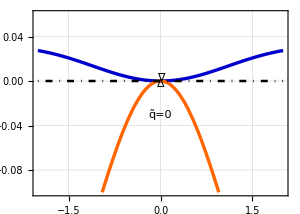

```mathematica
(*--------------------low rmax---------------------------*)
Subscript[ρ, 0]=0.5;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;
(*---------------------------------numetrical solution logistic normal------------------------------------*)
sol1=NDSolve[{u'[t]==u[t]*G1n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*(*---------------------------------numetrical solution allee normal------------------------------------*)
sol2=NDSolve[{u'[t]==u[t]*G3n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];*)

(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*(*---------------------------------numetrical solution allee trade off------------------------------------*)
sol4=NDSolve[{u'[t]==u[t]*G3[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];*)

(*---Fitness landscape normal logistic---*)

C1=Plot[Evaluate@{G1n[ϕ,p[9000]/. sol1[[1]],q[9000]/. sol1[[1]],u[9000]/. sol1[[1]],v[9000]/. sol1[[1]]],G2n[ϕ,p[9000]/. sol1[[1]],q[9000]/. sol1[[1]],u[9000]/. sol1[[1]],v[9000]/. sol1[[1]]]},{ϕ,-2,2},PlotRange->{{-2,2},{-0.1,0.06}},PlotStyle->{{blue,Thickness[0.008]},{orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"","Fitness"},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{0,-0.003}],FontSize->18,Bold],Style[Text["∇",{0,0.003}],FontSize->18,Bold],Style[Text["q̃=0",{0,-0.03}],FontSize->18]}];
(*---Additional graphics---*)
k=Plot[x=0,{x,-2,2},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k1=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{0,-0.075},{0,-0.005}}]}];*)
fig11=Show[C1,k(*,k1*)]
```

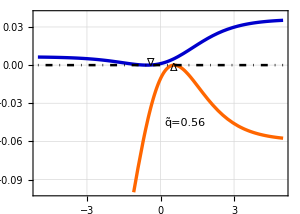

```mathematica
Subscript[ρ, 0]=0.5;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;
(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---Fitness landscape tradeoff logistic---*)
C2=Plot[Evaluate@{G1[ϕ,p[9000]/. sol3[[1]],q[9000]/. sol3[[1]],u[9000]/. sol3[[1]],v[9000]/. sol3[[1]]],G2[ϕ,p[9000]/. sol3[[1]],q[9000]/. sol3[[1]],u[9000]/. sol3[[1]],v[9000]/. sol3[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.1,0.04}},PlotStyle->{{blue,Thickness[0.008]},{orange,Thickness[0.008]} },Axes->False(*,FrameLabel->{"",""}*),LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["∇",{-0.45,0.002}],FontSize->18,Bold],Style[Text["Δ",{0.54,-0.002}],FontSize->18,Bold],Style[Text["q̃=0.56",{1,-0.045}],FontSize->18,Background->White](*,Style[Text["p̃=-0.91",{-2,-0.07}],FontSize->18,Background->White]*)}];

(*---Additional graphics---*)
k=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k1=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2,-0.07},{-0.54,-0.002}}]}];
k2=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{2.5,-0.07},{0.56,-0.005}}]}];*)
fig12=Show[C2,k(*,k1,k2*)]
```

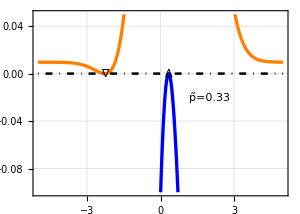

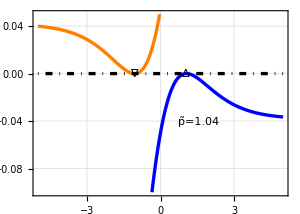

```mathematica
Subscript[ρ, 0]=0.5;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;

(*---------------------------------numetrical solution logistic normal------------------------------------*)
sol1=NDSolve[{u'[t]==u[t]*G1n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution allee normal------------------------------------*)
sol2=NDSolve[{u'[t]==u[t]*G3n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution allee trade off------------------------------------*)
sol4=NDSolve[{u'[t]==u[t]*G3[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
(*---Fitness landscape normal Allee---*)

C3=Plot[Evaluate@{G3n[ϕ,p[9000]/. sol2[[1]],q[9000]/. sol2[[1]],u[9000]/. sol2[[1]],v[9000]/. sol2[[1]]],G2n[ϕ,p[9000]/. sol2[[1]],q[9000]/. sol2[[1]],u[9000]/. sol2[[1]],v[9000]/. sol2[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.1,0.05}},PlotStyle->{{Blue,Thickness[0.008]},{Orange,Thickness[0.008]} },Axes->False(*,FrameLabel->{"",""}*),LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{0.33,0}],FontSize->18,Bold],Style[Text["∇",{-2.28,0}],FontSize->18,Bold],Style[Text["p̃=0.33",{2,-0.02}],FontSize->18,Background->White]}];
(*---Additional graphics---*)
j=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k3=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{3,-0.05},{0,-0.0035}}]}];
k4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2.2,-0.05},{-0.94,-0.0035}}]}];*)
fig13=Show[C3,j(*,k3,k4*)]

(*---Fitness landscape tradeoff Allee---*)
C4=Plot[Evaluate@{G3[ϕ,p[9000]/. sol4[[1]],q[9000]/. sol4[[1]],u[9000]/. sol4[[1]],v[9000]/. sol4[[1]]],G2[ϕ,p[9000]/. sol4[[1]],q[9000]/. sol4[[1]],u[9000]/. sol4[[1]],v[9000]/. sol4[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.1,0.05}},PlotStyle->{{Blue,Thickness[0.008]},{Orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"",""},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["∇",{-1.09,0}],FontSize->18,Bold],Style[Text["Δ",{1.04,0}],FontSize->18,Bold],Style[Text["p̃=1.04",{1.55,-0.04}],FontSize->18,Background->White]}];

(*---Additional graphics---*)
j=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.008],DotDashed}];
(*k3=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{3,-0.05},{0,-0.0035}}]}];
k4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2.2,-0.05},{-0.94,-0.0035}}]}];*)
fig14=Show[C4,j(*,k3,k4*)]
```

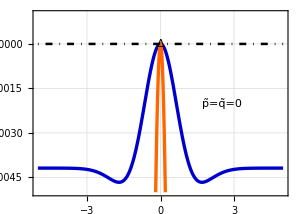

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;

(*---------------------------------numetrical solution logistic normal------------------------------------*)
sol1=NDSolve[{u'[t]==u[t]*G1n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution allee normal------------------------------------*)
sol2=NDSolve[{u'[t]==u[t]*G3n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution allee trade off------------------------------------*)
sol4=NDSolve[{u'[t]==u[t]*G3[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
(*---Fitness landscape normal logistic---*)

C1=Plot[Evaluate@{G1n[ϕ,p[9000]/. sol1[[1]],q[9000]/. sol1[[1]],u[9000]/. sol1[[1]],v[9000]/. sol1[[1]]],G2n[ϕ,p[9000]/. sol1[[1]],q[9000]/. sol1[[1]],u[9000]/. sol1[[1]],v[9000]/. sol1[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.005,0.001}},PlotStyle->{{blue,Thickness[0.008]},{orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"Evolutionary strategy","Fitness"},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{0,0}],FontSize->18,Bold](*,Style[Text["∇",{-1.71,-0.00466}],FontSize->18,Bold],Style[Text["∇",{1.71,-0.00466}],FontSize->18,Bold]*),Style[Text["p̃=q̃=0",{2.5,-0.002}],FontSize->18,Background->White]}];
(*---Additional graphics---*)
k=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k1=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{2,-0.002},{0.005,-0.0002}}]}];*)
fig21=Show[C1,k(*,k1*)]
```

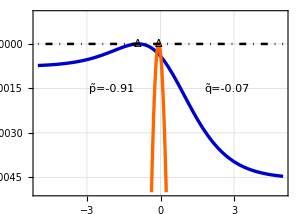

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;
(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
(*---Fitness landscape tradeoff logistic---*)
C2=Plot[Evaluate@{G1[ϕ,p[9000]/. sol3[[1]],q[9000]/. sol3[[1]],u[9000]/. sol3[[1]],v[9000]/. sol3[[1]]],G2[ϕ,p[9000]/. sol3[[1]],q[9000]/. sol3[[1]],u[9000]/. sol3[[1]],v[9000]/. sol3[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.005,0.001}},PlotStyle->{{blue,Thickness[0.008]},{orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"Evolutionary strategy",""},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{-0.911792,0}],FontSize->18,Bold],Style[Text["Δ",{-0.07,0}],FontSize->18,Bold],Style[Text["q̃=-0.07",{2.7,-0.0015}],FontSize->18,Background->White],Style[Text["p̃=-0.91",{-2,-0.0015}],FontSize->18,Background->White]}];

(*---Additional graphics---*)
k=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k1=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2,-0.002},{-0.9,-0.0001}}]}];
k2=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{2,-0.002},{-0.07,-0.0001}}]}];*)
fig22=Show[C2,k(*,k1,k2*)]
```

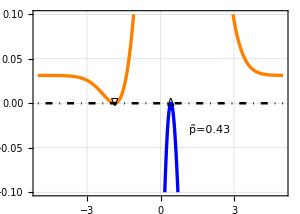

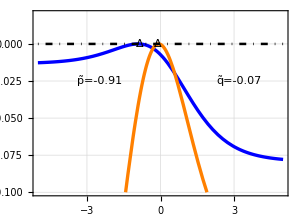

```mathematica
Subscript[ρ, 0]=0.75;Subscript[ρ, min]=0.25;κ=35;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.02;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=1.0;Subscript[k, 2]=1.0;Subscript[k, 3]=1.0;f=0.5;τ=1;

(*---------------------------------numetrical solution logistic normal------------------------------------*)
sol1=NDSolve[{u'[t]==u[t]*G1n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution allee normal------------------------------------*)
sol2=NDSolve[{u'[t]==u[t]*G3n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
(*---------------------------------numetrical solution allee trade off------------------------------------*)
sol4=NDSolve[{u'[t]==u[t]*G3[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G33[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,20000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---Fitness landscape normal Allee---*)

C3=Plot[Evaluate@{G3n[ϕ,p[9000]/. sol2[[1]],q[9000]/. sol2[[1]],u[9000]/. sol2[[1]],v[9000]/. sol2[[1]]],G2n[ϕ,p[9000]/. sol2[[1]],q[9000]/. sol2[[1]],u[9000]/. sol2[[1]],v[9000]/. sol2[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.1,0.1}},PlotStyle->{{Blue,Thickness[0.008]},{Orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"Evolutionary strategy",""},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{0.43,0}],FontSize->18,Bold],Style[Text["∇",{-1.9,0}],FontSize->18,Bold],Style[Text["p̃=0.43",{2,-0.03}],FontSize->18,Background->White]}];
(*---Additional graphics---*)
j=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k3=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{3,-0.05},{0,-0.0035}}]}];
k4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2.2,-0.05},{-0.94,-0.0035}}]}];*)
fig23=Show[C3,j(*,k3,k4*)]

(*---Fitness landscape tradeoff Allee---*)
C4=Plot[Evaluate@{G3[ϕ,p[9000]/. sol4[[1]],q[9000]/. sol4[[1]],u[9000]/. sol4[[1]],v[9000]/. sol4[[1]]],G2[ϕ,p[9000]/. sol4[[1]],q[9000]/. sol4[[1]],u[9000]/. sol4[[1]],v[9000]/. sol4[[1]]]},{ϕ,-5,5},PlotRange->{{-5,5},{-0.1,0.02}},PlotStyle->{{Blue,Thickness[0.008]},{Orange,Thickness[0.008]} },Axes->False,(*FrameLabel->{"Evolutionary strategy",""},*)LabelStyle->{FontSize->18},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->1.5/2.1,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],ImageSize->300,Epilog->{Style[Text["Δ",{-0.85,0}],FontSize->18,Bold],Style[Text["Δ",{-0.1,0}],FontSize->18,Bold],Style[Text["p̃=-0.91",{-2.5,-0.025}],FontSize->18,Background->White],Style[Text["q̃=-0.07",{3.2,-0.025}],FontSize->18,Background->White]}];

(*---Additional graphics---*)
j=Plot[x=0,{x,-5,5},PlotStyle->{GrayLevel[0],Thickness[0.006],DotDashed}];
(*k3=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{3,-0.05},{0,-0.0035}}]}];
k4=Graphics[{Arrowheads[0.05],Thickness[0.004],Arrow[{{-2.2,-0.05},{-0.94,-0.0035}}]}];*)
fig24=Show[C4,j(*,k3,k4*)]
```

```mathematica
g=Grid[{{"","",Style["logistic: Gaussian",25],Style["logistic: trade-off",25],Style["Allee: Gaussian",25],Style["Allee: trade-off",25]},{"","",Style["A",25],Style["B",25],Style["C",25],Style["D",25]},{Rotate[Style["low r_max",25],Pi/2],Item[Rotate[Style["mutant trait",25],Pi/2],Alignment->Center,ItemSize->{Automatic,4}],fig11,fig12,fig13,fig14},{SpanFromAbove,SpanFromAbove,Style["E",25],Style["F",25],Style["G",25],Style["H",25]},{Rotate[Style["high r_max",25],Pi/2],SpanFromAbove,fig21,fig22,fig23,fig24},{SpanFromAbove,SpanFromAbove,Style["resident trait",25],SpanFromLeft}},Alignment->Center,Spacings->{2,0}]
```

|  | logistic: Gaussian | logistic: trade-off | Allee: Gaussian | Allee: trade-off
 |  | A | B | C | D
low r_max | mutant trait | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  | E | F | G | H
high r_max |  | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  | resident trait |  |  |

```mathematica
Export[SystemDialogInput["FileSave","fit_steady_state.pdf"],g,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\user\Dropbox\SANTANA\P7_G function\Mondal_allee effect\fit_steady_state.pdf